附录

## Mathematica简介

Mathematica 是一个强大的符号运算和数值计算的软件系统。它本身系统功能强大，也很复杂，但从入门角度来看，还是非常容易的，特别地，Mathematica提供了非常系统的帮助，可以直接通过修改和运行帮助中的示例快速掌握。

## Section. Mathematica Notebooks笔记

Mathematica提供了一个用户操作环境-笔记（notebook，扩展名nb），通过笔记可以输入命令，执行后输出结果。笔记本的功能丰富，可以进行各种各式的编排，包括图形，文本，数学公式等等。笔记本通过单元（cell）来组织不同的类型的内容，就是大家看到的右侧的”]”标记。单元可以嵌套，默认情况下单元的分组是自动进行的，用户也可以通过菜单自主分组。分组的单元可以通过鼠标双击展开或收起，方便查看。
可以在任何位置创建一个单元，当鼠标光标显示为横线状是，就可以输入内容了，默认情况下的输入是代码各式。你现在就可以在这个文本单元下面移动鼠标，等鼠标变为短横线是点击，输入测试代码。

```mathematica
a=Sin[1]
```

作为代码输入的命令，可以是一条，也可以是多条。要执行一个cell里面的命令，按shift+回车键。如果命令正确，马上回得到输出结果。

## Section. 基本操作

基本运算符包括+[add], -[subtract], *[multiply], /[divide], ^[exponentiate]，Sqrt[ ]，Mathematica区分大小写，最常用的数据类型是列表-list，基本数据类型包括数值，字符串等，变量不需要定义可以直接用。数组的下标从1开始，而不是很多程序语言中的从0开始。很重要一点，mathematica的函数参数是用方括号来引用，而不是我们平常熟悉的圆括号。现在通过例子来看一下(你可以随时修改示例中的数值，然后按shift+回车键执行它）。

```mathematica
1+5+32*43/34^3
```

29650/4913

Mathematica总是给出精确值（有理式），我们可以让它计算出具体值来，用一个“N”函数：

```mathematica
N[1+5+32*43/34^3]
```

6.03501

N意味着number。N函数还可以更简单的方式来使用，看下面，//操作。

```mathematica
1+5+32*43/34^3//N
```

6.03501

### Caution on Mathematica Input Syntax

Mathematica的强大体现在众多的内置函数上。内置函数首字母大写，参数用方括号括起来。圆括号用于组织表达式的顺序，花括号{}用于表示列表和数组。变量乘法，可以用*，也可以用空格代替（数学中经常用a b=c，表示a乘以b=c），如果是一个数字开头乘以某变量，空格都可以略去，比如2a.

```mathematica
a=b=15;(*;表示不输出命令执行的结果*)
2 a b
```

450

特别注意，执行后所定义的变量就会一直存储在内存中，直到退出mathematica。在一个笔记中定义了变量a，在另一个笔记中也可以直接用a，注意看下面的例子：

```mathematica
Clear[a];(*Clear命令清除内存的变量a*)
b=2a
a=3
b
```

2 a

3

6

大家已经看到，先清除了a定义，则b的值为2a，当我给a赋值3后，b的值自动更新为2*3=6.为避免出现我们不希望的结果，尽量少用直接赋值的操作，可以用mathematica的替代规则，看下面.

### 替代规则

命名一个表达式，比如下面的e1，表示了一个表达式，在我们需要计算这个表达式的时候，把其中的x替换一下就可以，替换操作符:‘/.’

```mathematica
e1=x+Sin[x] Cos[x^3]/Exp[x]
```

```mathematica
e1 /. x->1.5
```

1.28346

“->”表示一个规则，如果是一个规则，可以直接写出来，如果是多个规则，就用一个花括号括起来。

```mathematica
e2 = e1 /. {x->a + Sin[b]}
```

a+sin(b)+ⅇ^(-a-sin(b)) cos((a+sin(b))^3) sin(a+sin(b))

替换 a=1 and b=2 in expression e2.

```mathematica
e2 /. {a->1, b->2}
```

1+sin(2)+ⅇ^(-1-sin(2)) cos((1+sin(2))^3) sin(1+sin(2))

利用N函数获得数值结果：

```mathematica
N[e2 /. {a->1, b->2}]
```

2.01825

命令后面加分号表示不输出计算结果。

### 系统保留的符号

系统预留的符号定义如下，可以在程序中直接用：

```mathematica
{E,I, Pi, GoldenRatio}//N
```

{2.71828,0.+1. ⅈ,3.14159,1.61803}

### 使用内置函数

可以通过mathematica的帮助，查询不同领域的内置函数，这里是一些简单的示例。提升：鼠标放在函数名上，会出现提升，点击查看函数的简单说明或详细帮助。

```mathematica
Simplify[a^2+3 a+(a+b) a]
```

a (2 a+b+3)

```mathematica
Expand[a^2+3 a+(a+b) a]
```

2 a^2+b a+3 a

求导：

```mathematica
e1=x+Sin[x] Cos[x^3]/Exp[x];
de1=D[e1,x]
```

1+ⅇ^-x Cos[x] Cos[x^3]-ⅇ^-x Cos[x^3] Sin[x]-3 ⅇ^-x x^2 Sin[x] Sin[x^3]

积分：

```mathematica
e2=Integrate[de1,x]
NIntegrate[e1,{x,0,1}]
```

x+ⅇ^-x Cos[x^3] Sin[x]

0.724231

## Section. 列表和矩阵

mathematica的括号用法，初学者要注意，但也不要陷于括号而花费太多的精力，可以在逐步使用过程中提高理解。

### Lists列表

有6个元素的一维列表：

```mathematica
s={1,3,Sin[bb], 2*x, 5, (3*y)/x^3}
```

{1,3,sin(bb),2 x,5,(3 y)/x^3}

计算列表的长度

```mathematica
Length[s]
```

6

提取列表中的元素，双方括号，最外层方括号相当于函数调用，内层方括号是元素序号（从1开始），如果是多个元素，用{}括起来元素序号。

```mathematica
ss = s[[{3,4,6}]]
```

{sin(bb),2 x,(3 y)/x^3}

大多数的代数运算可以直接应用于列表的所有元素，如求导：

```mathematica
D[ss,x]
```

{0,2,-(9 y)/x^4}

多维列表：

```mathematica
a={{1},{2,3,4},s}
```

{{1},{2,3,4},{1,3,sin(bb),2 x,5,(3 y)/x^3}}

```mathematica
Length[a]
```

3

提取多维列表的第二行：

```mathematica
a[[2]]
```

{2,3,4}

提取列表的第3行的第6个元素：

```mathematica
a[[3,6]]
```

(3 y)/x^3

压平多维列表可以用Flatten函数（移除所有内部的花括号）：

```mathematica
b=Flatten[a]
```

{1,2,3,4,1,3,sin(bb),2 x,5,(3 y)/x^3}

由列表生成多维数组：鼠标放在函数名上，可以看到帮助信息。

```mathematica
Partition[b,3]
```

(1 | 2 | 3
4 | 1 | 3
sin(bb) | 2 x | 5)

```mathematica
Partition[b,4]
```

(1 | 2 | 3 | 4
1 | 3 | sin(bb) | 2 x)

### 数组array

数组是特殊的列表，每行的列数相同：

```mathematica
m = {{1,2,3},{5,6,7},{9,10,11}}
```

(1 | 2 | 3
5 | 6 | 7
9 | 10 | 11)

下面不是数组：

```mathematica
a={{1},{2,3},{4,5,6}}
```

{{1},{2,3},{4,5,6}}

对数组可以应用所有的矩阵运算函数：

```mathematica
mt = Transpose[m]
```

(1 | 5 | 9
2 | 6 | 10
3 | 7 | 11)

矩阵点积

```mathematica
mt.m
```

(107 | 122 | 137
122 | 140 | 158
137 | 158 | 179)

乘法*操作，为元素层次element level的相乘

```mathematica
mt* m
```

(1 | 10 | 27
10 | 36 | 70
27 | 70 | 121)

提取矩阵的某行：

```mathematica
m = {{1,2,3,4},{5,6,7,8},{9,10,11,12}};m//MatrixForm
```

(1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12)

```mathematica
m2 = m[[2]]
```

{5,6,7,8}

第二行第四列：

```mathematica
m[[2, 4]]
```

8

提取第二列：

```mathematica
c2 = m[[All,2]](*All 表示所有行*)
```

{2,6,10}

符号矩阵：

```mathematica
m = {{y, 2*x}, {(3*y)/x^3, 4*y}}; MatrixForm[m]
```

(y | 2 x
(3 y)/x^3 | 4 y)

矩阵的行列式：

```mathematica
Det[m]
```

4 y^2-(6 y)/x^2

矩阵的逆：

```mathematica
mi = Inverse[m]; MatrixForm[mi]
```

((4 y)/(4 y^2-(6 y)/x^2) | -(2 x)/(4 y^2-(6 y)/x^2)
-(3 y)/(x^3 (4 y^2-(6 y)/x^2)) | y/(4 y^2-(6 y)/x^2))

验证逆矩阵：

```mathematica
Simplify[mi.m]
```

(1 | 0
0 | 1)

矩阵求导（对每一个元素）和积分：

```mathematica
D[m,y]
```

(1 | 0
3/x^3 | 4)

```mathematica
Integrate[m,x]
```

(x y | x^2
-(3 y)/(2 x^2) | 4 x y)

### 通过Table命令创建列表list

Table命令很适合创建各种列表和矩阵：

```mathematica
m = Table[0,{3},{5}]
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
z=Table[(i+j)/3^j,{i,1,3},{j,1,4}](*Table函数的第一个参数是元素表达式，后面的参数是变量范围，{i,1,3}表示变量i从1到3，即取值1,2,3，也可以简写为{i,3}*)
```

{{2/3,1/3,4/27,5/81},{1,4/9,5/27,2/27},{4/3,5/9,2/9,7/81}}

通过If语句创建复杂的列表：

```mathematica
z=Table[If[i>j,0,(i+j)/3^j],{i,1,4},{j,1,4}]
```

(2/3 | 1/3 | 4/27 | 5/81
0 | 4/9 | 5/27 | 2/27
0 | 0 | 2/9 | 7/81
0 | 0 | 0 | 8/81)

### 注意：列向量和行向量

mathematica不区分列向量和行向量，它根据运算环境来判定：

```mathematica
a = {1, 2, 3}; b = {4, 5, 6};
```

```mathematica
a . b
```

32

通过外积函数Outer计算两个向量：

```mathematica
ab = Outer[Times, a, b]; MatrixForm[ab]
```

(4 | 5 | 6
8 | 10 | 12
12 | 15 | 18)

显式定义列向量：

```mathematica
a = {{1}, {2}, {3}}; MatrixForm[a]
```

(1
2
3)

```mathematica
b = {{4, 5, 6}}
```

(4 | 5 | 6)

```mathematica
a . b
```

(4 | 5 | 6
8 | 10 | 12
12 | 15 | 18)

## Section. 解方程

方程用==连接左右两部分（一个等号=表示赋值操作）：

```mathematica
x^3 - 3 == 0
```

x^3-3==0

可以把方程用一个变量表示：

```mathematica
eq = x^3 - 3 == 0
```

x^3-3==0

Solve函数求解方程

```mathematica
sol=Solve[eq, x]
```

{{x→--3^(1/3)},{x→3^(1/3)},{x→(-1)^(2/3) 3^(1/3)}}

注意求解结果是二维数组，元素是一个规则（rule：->)

```mathematica
eq /. sol[[2]]
```

True

NSolve解方程的数值解，速度更快。

```mathematica
NSolve[x^3 - 3 == 0, x]
```

{{x→-0.721125-1.24902 ⅈ},{x→-0.721125+1.24902 ⅈ},{x→1.44225}}

求解线性或非线性方程组：

```mathematica
Clear[x,y,z];
eqn1 = x + 2y + 3z == 41; 
eqn2 = 5x + 5y + 4z == 20; 
eqn3 = 3y + 4z == 125; 
sol = Solve[{eqn1, eqn2, eqn3}, {x, y, z}]
```

{{x→-527/13,y→635/13,z→-70/13}}

```mathematica
a=N[Sin[x y]Cos[y^z]/.sol[[1]]]
```

-0.810238

Ka=b形式的线性方程组，用LinearSolve[K,b]速度更快.

```mathematica
K={{2,4,6},{7,9,2},{1,2,13}};
R={1,2,3};
LinearSolve[K,R]
```

{21/20,-13/20,1/4}

## Section. 绘图

Mathematica有很强的绘图功能，包括二维三维绘图。

```mathematica
p1 = Plot[Sin[x] Cos[x]/(1+x^2),{x,-2,2}];
```

可以把多个图绘制在一张上面：

```mathematica
de1 = D[Sin[x] Cos[x]/(1+x^2),x];
p2 = Plot[de1,{x,-2,2}, PlotStyle->{RGBColor[0,0,1]},
	DisplayFunction -> Identity];
Show[{p1,p2}];
```

下面的函数运行会出错：

```mathematica
Plot[D[Sin[x] Cos[x]/(1+x^2),x],{x,-2,2}];
```

因为Plot函数并不去计算它的参数，因此，需要如下来处理：

```mathematica
Plot[Evaluate[D[Sin[x] Cos[x]/(1+x^2),x]],{x,-2,2}];
```

两个变量可以绘制等值线图或三维图形

```mathematica
f=Sin[x]Cos[y]
```

Cos[y] Sin[x]

```mathematica
ContourPlot[f,{x,-π,π},{y,-π,π},PlotPoints->50]
```

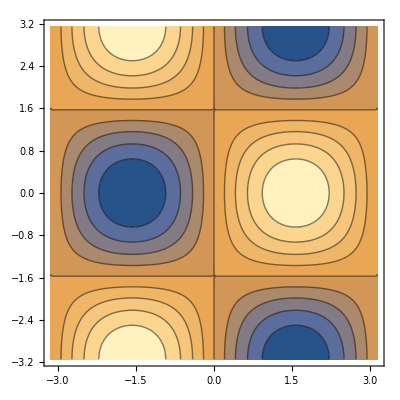

```mathematica
%25
```

```mathematica
Plot3D[f,{x,-π,π},{y,-π,π}]
```

## Section. 微分方程

DSolve命令求解微分方程：

```mathematica
?DSolve
```

DSolve[eqn, y, x] solves a differential equation for the function y, with independent variable x. DSolve[{eqn1, eqn2, ...  }, {y1, y2, ...  }, x] solves a list of differential equations. DSolve[eqn, y, {x1, x2, ... }] solves a partial differential equation. More…

举例：求解下面的微分方程+边界条件

(d^2 u)/dx^2+u+x=0 | 1<x<3
u(1)=2 | du/dx(3)=0

```mathematica
sol=DSolve[{D[u[x],{x,2}]+u[x]+x==0,u[1]==2,(D[u[x],x]/.x->3)==0},u[x],x]
```

{{u(x)→(-sin(1) sin(3) x-cos(1) cos(3) x+3 cos(3) cos(x)+3 sin(3) sin(x)+cos(1) sin(x)-cos(x) sin(1))/(cos(1) cos(3)+sin(1) sin(3))}}

检验结果

```mathematica
ux=u[x]/.sol[[1]]
```

(-sin(1) sin(3) x-cos(1) cos(3) x+3 cos(3) cos(x)+3 sin(3) sin(x)+cos(1) sin(x)-cos(x) sin(1))/(cos(1) cos(3)+sin(1) sin(3))

```mathematica
D[ux,{x,2}]+ux+x
```

x+(sin(1) cos(x)-3 cos(3) cos(x)-3 sin(3) sin(x)-cos(1) sin(x))/(cos(1) cos(3)+sin(1) sin(3))+(-sin(1) sin(3) x-cos(1) cos(3) x+3 cos(3) cos(x)+3 sin(3) sin(x)+cos(1) sin(x)-cos(x) sin(1))/(cos(1) cos(3)+sin(1) sin(3))

绘制结果

```mathematica
Plot[ux,{x,1,3}]
```

结果的一阶导数

```mathematica
Plot[Evaluate[D[ux,x]],{x,1,3}]
```

微分方程数值解NDSolve：

```mathematica
?NDSolve
```

NDSolve[eqns, y, {x, xmin, xmax}] finds a numerical solution to the ordinary differential equations eqns for the function y with the independent variable x in the range xmin to xmax. NDSolve[eqns, y, {x, xmin, xmax}, {t, tmin, tmax}] finds a numerical solution to the partial differential equations eqns. NDSolve[eqns, {y1, y2, ... }, {x, xmin, xmax}] finds numerical solutions for the functions yi. More…

x(d^2 u)/dx^2+u+x=0 | u(1)=2 | du/dx(3)=0

```mathematica
DSolve[{x D[u[x],{x,2}]+u[x]+x==0,u[1]==2,(D[u[x],x]/.x->3)==0},u[x],x]
```

NDSolve：

```mathematica
sol=NDSolve[{x D[u[x],{x,2}]+u[x]+x==0,u[1]==2,(D[u[x],x]/.x->3)==0},u[x],{x,1,3}]
```

{{u(x)→InterpolatingFunction[(1. | 3.),<>][x]}}

```mathematica
Plot[u[x]/.sol[[1]],{x,1,3}]
```

```mathematica
Plot[Evaluate[D[(u[x]/.sol[[1]]),x]],{x,1,3}];
```

## Section. 编程

### 定义自己的函数

格式

newFunctionName[var1_, var2_, ...] := Module[
		{localVar1, localVar2, …},
		statement 1;
		statement 2;
		⋮
		last statement
	]

函数名为避免和内置函数混淆，建议首字母用小写。注意Module内各部分的标点符号用法。

最简单函数定义：

oneLineFcn[var1_, var2_, ...] := expression involving vars

下面的例子计算厚壁桶切向和径向应力：

σ_t=(p_i r_i^2)/(r_0^2-r_i^2)(1+r_0^2/r^2)		σ_r=(p_i r_i^2)/(r_0^2-r_i^2)(1-r_0^2/r^2)

p_i 内压, r_i ， r_0 内外半径 r 是半径.

```mathematica
thickCylinderStresses[pi_, ri_, r0_, r_] :=
 Module[{c1, c2, σt, σr},
 	c1=pi ri^2/(r0^2 - ri^2);
 	c2=r0^2/r^2;
 	σt=c1(1+c2);
 	σr=c1(1-c2);
 	{σt, σr}
 ]
```

使用自定义函数， pi = 20, ri = 5, r0 = 15 and r = 10 ：

```mathematica
thickCylinderStresses[20,5,15,10]
```

{65/8,-25/8}

也可以用符号值：

```mathematica
{st,sr}=thickCylinderStresses[20,5,15,r]
```

{5/2 (1+225/r^2),5/2 (1-225/r^2)}

绘制结果：

```mathematica
Plot[{st,sr},{r,5,15},AxesLabel->{"r","Stress"}, PlotStyle->{{GrayLevel[0]},{GrayLevel[0.5]}}]
```

进一步的应用：

```mathematica
{st,sr}=thickCylinderStresses[20,ri,15,(ri+15)/2]
```

{(20 ri^2 (1+900/(15+ri)^2))/(225-ri^2),(20 ri^2 (1-900/(15+ri)^2))/(225-ri^2)}

厚壁桶变为薄壁桶

```mathematica
Plot[{st,sr},{ri,5,14},AxesLabel->{"ri","Stress"}, PlotStyle->{{GrayLevel[0.5]},{GrayLevel[0]}}]
```

薄壁桶切向应力显著：

```mathematica
Plot[{st,(20 (ri+15)/2)/(15-ri)},{ri,5,14},AxesLabel->{"ri","Stress"}, PlotStyle->{{GrayLevel[0]},{GrayLevel[0.5]}}]
```

### 高级应用

我们经常需要对函数或变量列表执行操作。许多内置函数被设计成直接对列表进行操作。然而，在许多情况下，仍然需要对数量列表执行某些操作。在传统的编程语言中，我们通常使用Do循环或类似的方法来执行这些操作。Mathematica有一个可以以类似方式使用的Do循环。然而，它也提供了许多其他优雅和更方便的方式来做同样的事情。Map、Thread和Apply是其中三个方便的函数。

```mathematica
data1={18.24,12.12,15.23,5.26};data2={12.24,19.16,35.07,23.46,-10.62,-7.43,2.62,10.42};
data3={8.23,8.96,8.35,9.16,8.05};
data4={8.12,8.26,8.34,9.01,9.11,8.95,7.29};
```

```mathematica
Total[data1]
```

50.85

```mathematica
Apply[Plus,data1]
```

50.85

```mathematica
Apply[Times,data1]
```

17709.8

```mathematica
Map[Sin,data1]
```

{-0.572503,-0.431695,0.459972,-0.853771}

```mathematica
average[n_]:=Apply[Plus,n]/Length[n]
```

```mathematica
average[data1]
```

12.7125

```mathematica
allData={data1, data2,data3,data4}
```

{{18.24,12.12,15.23,5.26},{12.24,19.16,35.07,23.46,-10.62,-7.43,2.62,10.42},{8.23,8.96,8.35,9.16,8.05},{8.12,8.26,8.34,9.01,9.11,8.95,7.29}}

```mathematica
averages=Map[average,allData]
```

General::spell1: Possible spelling error: new symbol name "TraditionalForm`averages" is similar to existing symbol "TraditionalForm`average".

{12.7125,10.615,8.55,8.44}

```mathematica
averageReturns=Map[Apply[Plus,#]/Length[#]&,allData](*Apply[Plus,#]/Length[#]&，匿名函数的定义*)
```

{12.7125,10.615,8.55,8.44}

# 代表函数形参， (&)表示函数定义结束

```mathematica
f=Subscript[x, 1] Subscript[x, 2]+ Sin[Subscript[x, 3]]Cos[Subscript[x, 4]];
pt={1.1,2.23,3.2,4.556};
vars={Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]};
```

可以这样实现：

```mathematica
f/.{Subscript[x, 1]->1.1,Subscript[x, 2]->2.23,Subscript[x, 3]->3.2,Subscript[x, 4]->4.556}
```

2.46209

下面方法更简洁

```mathematica
Thread[vars->pt]
```

{x_1→1.1,x_2→2.23,x_3→3.2,x_4→4.556}

```mathematica
f/.Thread[vars->pt]
```

2.46209

## Section. 功能包package

Need函数调用包，新版本中很多包已经包含进mathematica系统。

## Section. On-Line Help

Mathematica contains a complete on-line help system. The Help menu provides access to all Mathematica features. In fact the entire Mathematica 3.0 book is on-line. In addition you can obtain information about any command by typing '?' followed by the command name. This form also supports use of wild-cards. For example to get a listing of all commands that start with letter G type

```mathematica
?G*
```

GenerateAsymmetricKeyPair[] 为使用公钥加密函数随机产生一个 PrivateKey 和对应的 PublicKey 对象.
GenerateAsymmetricKeyPair[opts] 使用指定的选项随机产生私钥和公钥.

Detailed instructions about a specific command can be obtained by typing ? followed by the command name. For example

```mathematica
?GaussPoints
```

GaussPoints is an option for NIntegrate. With GaussPoints -> n, the Gaussian part of Gauss-Kronrod quadrature uses n points. With GaussPoints -> Automatic, an internal algorithm chooses the number of points.